```mathematica
<<myFunctionsMathematica8.m
```

{Temporary}

```mathematica
bestzero[n_]:=1/2+I*t[n]
```

```mathematica
strm=OpenRead["2000 better zeros copy 2"];
zrs=ReadList[strm];
zero[n_]:=zrs[[n]]
```

```mathematica
Length[zrs]
```

5051

```mathematica
bestzero[5000]
```

1/2+ⅈ t[5000]

seconds 45.08349

{0.,Indeterminate}

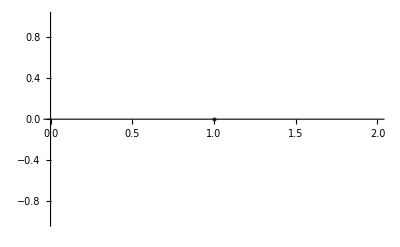

barryzerosprecision1000no8

```mathematica
stream=OpenWrite["barryzerosprecision1000no8"];
precision=1000;
errors={};

start=SessionTime[];
For[n=0,n<1,n++;
startcenter=zero[n];
zr=FindRoot[Zeta[u],{u,startcenter},PrecisionGoal->precision,WorkingPrecision->2*precision][[1,2]];
imzr=Im[zr];
Write[stream,{n,imzr}];
Print["seconds ",SessionTime[]-start];
error=Abs[Zeta[1/2+I*imzr]];
errors=Append[errors,error]];
Print[{Max[errors],Log[Abs[1/2-Re[zr]]]}];
Print[ListPlot[errors]];
Close[stream]
```

```mathematica
stream=OpenAppend["barryzerosprecision1000no8"];
precision=1000;
errors={};
start=SessionTime[];
For[n=1,n<2,n++;
startcenter=zero[n];
zr=FindRoot[Zeta[u],{u,startcenter},PrecisionGoal->precision,WorkingPrecision->2*precision][[1,2]];
imzr=Im[zr];
Write[stream,{n,imzr}];
Print["seconds ",SessionTime[]-start];
error=Abs[Zeta[1/2+I*imzr]];
errors=Append[errors,error]];
Print[ListPlot[errors]];
Close[stream]
```

seconds 48.38513

-Graphics-

barryzerosprecision1000no8

seconds 48.43728

seconds 102.1939

seconds 158.89027

seconds 212.65188

seconds 268.16121

seconds 322.89779

seconds 378.19635

seconds 433.00981

seconds 487.78118

seconds 543.32838

seconds 598.63311

seconds 653.82513

seconds 707.759231

seconds 761.449833

seconds 814.714428

seconds 872.765663

seconds 931.175807

seconds 985.267914

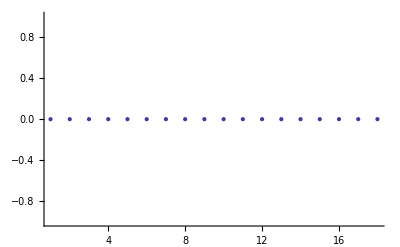

barryzerosprecision1000no8

```mathematica
stream=OpenAppend["barryzerosprecision1000no8"];
precision=1000;
errors={};
start=SessionTime[];
For[n=2,n<20,n++;
startcenter=zero[n];
zr=FindRoot[Zeta[u],{u,startcenter},PrecisionGoal->precision,WorkingPrecision->2*precision][[1,2]];
imzr=Im[zr];
Write[stream,{n,imzr}];
Print["seconds ",SessionTime[]-start];
error=Abs[Zeta[1/2+I*imzr]];
errors=Append[errors,error]];
Print[ListPlot[errors]];
Close[stream]
```

```mathematica
Max[errors]
```

2.×10^-1996

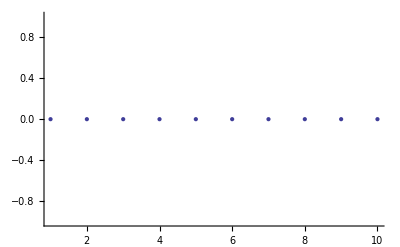

seconds 591.10486

barryzerosprecision1000no8

```mathematica
stream=OpenAppend["barryzerosprecision1000no8"];
precision=1000;
errors={};
start=SessionTime[];
For[n=20,n<30,n++;
startcenter=zero[n];
zr=FindRoot[Zeta[u],{u,startcenter},PrecisionGoal->precision,WorkingPrecision->2*precision][[1,2]];
imzr=Im[zr];
Write[stream,{n,imzr}];

error=Abs[Zeta[1/2+I*imzr]];
errors=Append[errors,error]];
Print[ListPlot[errors]];
Print["seconds ",SessionTime[]-start];
Close[stream]
```

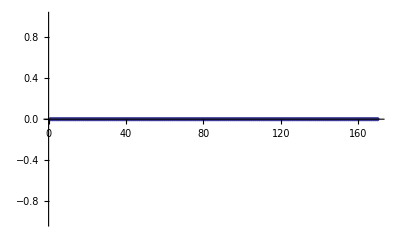

seconds 11474.37153

barryzerosprecision1000no8

```mathematica
stream=OpenAppend["barryzerosprecision1000no8"];
precision=1000;
errors={};
start=SessionTime[];
For[n=30,n<200,n++;
startcenter=zero[n];
zr=FindRoot[Zeta[u],{u,startcenter},PrecisionGoal->precision,WorkingPrecision->2*precision][[1,2]];
imzr=Im[zr];
Write[stream,{n,imzr}];

error=Abs[Zeta[1/2+I*imzr]];
errors=Append[errors,error]];
Print[ListPlot[errors]];
Print["seconds ",SessionTime[]-start];
Close[stream]
```